# Nakagami channel detection probability (large SNR comparison)

This notebook tests the accuracy of the large SNR approximate method against Annamalai’s exact method for cooperative networks of energy detectors operating on Nakagami-faded channels.

### Copyright notice

Copyright (C) 2012 Donagh Horgan.
Email: donaghh@rennes.ucc.ie.

This program is free software : you can redistribute it and/or modify
it under the terms of the GNU General Public License as published by
the Free Software Foundation, either version 3 of the License, or
(at your option) any later version.

This program is distributed in the hope that it will be useful,
but WITHOUT ANY WARRANTY; without even the implied warranty of
MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See 
COPYING for more details.

You should have received a copy of the GNU General Public License
along with this program. If not, see http://www.gnu.org/licenses.

### Version information

27/06/2012
1.0

### Changelog

Version 1.0: This version was used in the submitted version of the paper.

## Set up

Clear all symbol values and load function definitions:

```mathematica
Unprotect["Global`*"];
ClearAll["Global`*"];
```

```mathematica
path=NotebookDirectory[];
SetDirectory[path];
<<definitions.m
<<plots.m
```

## Variables

Here, we define the ranges of values to be used for each parameter.

```mathematica
nRange={1,2,3,4,5,10,20};
mRange={0.5,1,1.5,2};
samplesRange={1000,10000,50000};
snrdbRange=Range[0,-10,-1];
snrRange=10^(snrdbRange/10);
pfRange={49/100,30/100,20/100,10/100,5/100,1/100,5/1000,1/1000,5/10000,1/10000,5/100000,1/100000};
```

Here, we select n and m so that m n ∈ I:

```mathematica
{nRange,mRange,mnRange}=Select[Flatten[Table[{nRange⟦i⟧,mRange⟦j⟧,nRange⟦i⟧ mRange⟦j⟧},{i,Length[nRange]},{j,Length[mRange]}],1],Ceiling[##[[3]]]==##[[3]]&]//Transpose;
```

## Calculations

Calculate the probability of detection, for each set of parameter values defined previously, using the exact and approximate methods:

```mathematica
exact=Table[ProbabilityOfDetection[M,snr,λ[M,pf,nRange[[mn]],Method->"Exact"],nRange[[mn]],ChannelType->{"Nakagami",mRange[[mn]]},Method->"ExactAnnamalai",DatabaseLookup->True],{snr,snrRange},{mn,Length[mnRange]},{M,samplesRange},{pf,pfRange}];
```

```mathematica
approx=Table[ProbabilityOfDetection[M,snr,λ[M,pf,nRange[[mn]],Method->"Approximate"],nRange[[mn]],ChannelType->{"Nakagami",mRange[[mn]]},Method->"ApproximateLargeSNR"]//N,{snr,snrRange},{mn,Length[mnRange]},{M,samplesRange},{pf,pfRange}];
```

Calculate various error metrics:

```mathematica
error=exact-approx;
absError=Abs[error];
relError=error/exact;
absRelError=Abs[relError];
```

## Results

### Detection probabilities

Plots of detection probabilities against signal to noise ratio, for the defined parameter sets, using the exact and approximate methods:

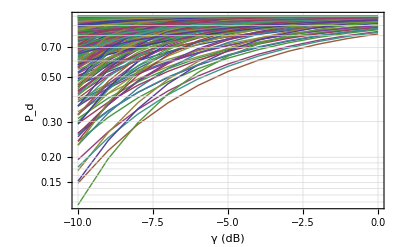
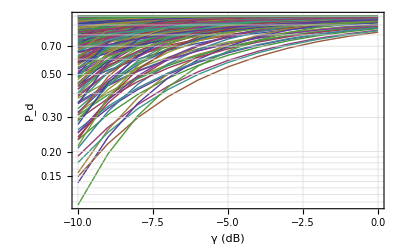

```mathematica
Table[CustomPlot[snrdbRange,y,{"γ (dB)","P_d"}],{y,{exact,approx}}]
```

### Error statistics

#### Error and absolute error

Probability density function of the approximation error:

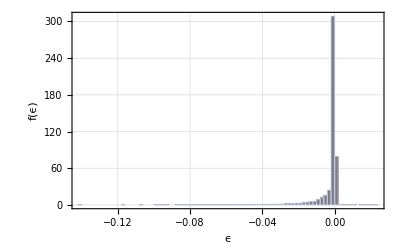

```mathematica
CustomHistogram[error,{"ϵ","f(ϵ)"}]
```

Histogram statistics:

```mathematica
StatsTable[error]
```

| μ | σ
 | -0.00326388 | 0.00951406

Largest errors:

```mathematica
MaxErrorsTable[absError,10]
```

γ (dB) | n | m | M | pf | ϵ | ϵ_r
-10. | 1. | 1. | 1000. | 0.49 | -0.140035 | -0.163922
-9. | 1. | 1. | 1000. | 0.49 | -0.11731 | -0.133585
-10. | 1. | 2. | 1000. | 0.3 | -0.117051 | -0.141661
-10. | 2. | 0.5 | 1000. | 0.49 | -0.106029 | -0.119141
-10. | 1. | 2. | 1000. | 0.2 | -0.0980609 | -0.12861
-8. | 1. | 1. | 1000. | 0.49 | -0.0973468 | -0.108276
-10. | 1. | 2. | 1000. | 0.49 | -0.0949971 | -0.104984
-10. | 1. | 1. | 1000. | 0.3 | -0.0948219 | -0.124956
-9. | 1. | 2. | 1000. | 0.3 | -0.0929837 | -0.107005
-9. | 2. | 0.5 | 1000. | 0.49 | -0.0875713 | -0.0963139

#### Relative error and absolute relative error

Probability density function of the relative approximation error:

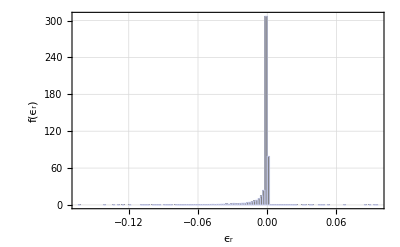

```mathematica
CustomHistogram[relError,{"ϵ_r","f(ϵ_r)"}]
```

Histogram statistics:

```mathematica
StatsTable[relError]
```

| μ | σ
 | -0.00371826 | 0.0117921

Largest relative errors:

```mathematica
MaxErrorsTable[absRelError,10]
```

γ (dB) | n | m | M | pf | ϵ | ϵ_r
-10. | 1. | 1. | 1000. | 0.49 | -0.140035 | -0.163922
-10. | 1. | 2. | 1000. | 0.3 | -0.117051 | -0.141661
-9. | 1. | 1. | 1000. | 0.49 | -0.11731 | -0.133585
-10. | 1. | 2. | 1000. | 0.2 | -0.0980609 | -0.12861
-10. | 1. | 1. | 1000. | 0.3 | -0.0948219 | -0.124956
-10. | 2. | 0.5 | 1000. | 0.49 | -0.106029 | -0.119141
-8. | 1. | 1. | 1000. | 0.49 | -0.0973468 | -0.108276
-9. | 1. | 2. | 1000. | 0.3 | -0.0929837 | -0.107005
-9. | 1. | 1. | 1000. | 0.3 | -0.0843749 | -0.105912
-10. | 1. | 2. | 1000. | 0.49 | -0.0949971 | -0.104984